# Introduction to Lists

Math 250 - Mathematical Computing
Christopher Hanusa

## 2.1 Aim

The aim of this tutorial is to introduce the user to lists, highlight important commands which generate lists, and show multiple ways to present lists in digestible formats.

These tutorials are meant to be interactive.  You should be playing around with the inputs to try to see what changes in the output when you change the inputs.

## 2.2 Lists by hand

Every list is surrounded by a left brace { and a right brace }.  Entries of the list are separated by commas.

```mathematica
{1,2,3}
```

{1,2,3}

### Example

Example 2.2.1. Create a list of the coordinates (2,1), (3,3), and (4,2) that is a variable named coordinates.

```mathematica
coordinates={{2,1},{3,3},{4,2}}
```

{{2,1},{3,3},{4,2}}

```mathematica
coordinates
```

{{2,1},{3,3},{4,2}}

We will learn how to plot the coordinates later.

## 2.3 Syntax

Every programming language has special words that perform a task when they are evaluated.  They are called commands. 
In Tutorial 1 you met a few, including Plot which plots the graph of a function.

In order to use these commands, you need to know how they work.  
That involves understanding their syntax:

What inputs (parameters) does the command need?

What type of output does the command give?

What is the rule that is applied to the inputs to give the output?

In a paper notebook, write down the syntax for the commands you learn today and the ones you see regularly.

## 2.4 Simple Lists using Range

Use Range to create a list of evenly spaced numbers.

A Range command has between 1 and 3 inputs.  Its output is a list.  Compare the following inputs and outputs.

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Range[2,10]
```

{2,3,4,5,6,7,8,9,10}

```mathematica
Range[0,10,2]
```

{0,2,4,6,8,10}

When there is only one input n, the output will be a list of integers starting at 1 and increasing to n.
When there are two inputs m and n, the output will be the list of integers starting at m and increasing to n.
When there are three inputs m, n, and incr, then the output will be the list of integers starting at m and increasing to n in increments of incr.

### Examples

Example 2.4.1. What do you think will happen if the input to Range is a negative integer?

```mathematica
Range[-10]
```

{}

Example 2.4.2. What list do you expect each of the following commands to give?

```mathematica
Range[1]
```

{1}

```mathematica
Range[3,4,2/5]
```

{3,17/5,19/5}

```mathematica
Range[100,0,-8]
```

{100,92,84,76,68,60,52,44,36,28,20,12,4}

Example 2.4.3. What Range commands will give the following lists?

```mathematica
{-5,-4,-3,-2}
```

```mathematica
Range[-5,-2]
```

{-5,-4,-3,-2}

```mathematica
Range[-5,-2,1]
```

{-5,-4,-3,-2}

```mathematica
{17,27,37,47,57,67,77,87,97}
```

```mathematica
Range[17,97,10]
```

{17,27,37,47,57,67,77,87,97}

## 2.5 Algorithmic lists using Table

The Table command generates a list based on a function you specify.

Consider the syntax of a Table command:

```mathematica
Table[x^2,{x,0,5}]
```

{0,1,4,9,16,25}

There are always two inputs to Table,

A function (x^2)

A list ({x,0,5})

The output of Table is always a list.

The list specifies the values of x that will be inserted into the function. 
The first element in the list is always the variable that is modified by the function (in this case, x).

If the list is of length two, such as {x,5}, then the values of x that will be inserted are between 1 and that value (5).

```mathematica
Table[x^2,{x,5}]
```

{1,4,9,16,25}

If the list is of length three, such as {x,-1,5}, then the values of x that will be inserted are from the first number to the second number.

```mathematica
Table[x^2,{x,-1,5}]
```

{1,0,1,4,9,16,25}

If the list is of length four, such as {x,0,10,2}, then the values of x that will be inserted are from the first number to the second number by increments of the last number.

```mathematica
Table[x^2,{x,0,10,2}]
```

{0,4,16,36,64,100}

There also is one NEW type of allowed input.
If the list is contains a variable and another nested list, such as {x,{0,10,2}}, then the values of x that will be inserted are exactly the values in this nested list, output in that order.

```mathematica
Table[x^2,{x,{0,10,2}}]
```

{0,100,4}

### Examples

Example 2.5.1. What list do you expect each of the following commands to give?

```mathematica
Table[-z,{z,1.5,3.5,0.5}]
```

{-1.5,-2.,-2.5,-3.,-3.5}

```mathematica
Table[Sqrt[b],{b,{1,10,Pi}}]
```

{1,√10,√π}

```mathematica
Table[Sqrt[b],{b,1,10,Pi}]
```

```mathematica
Table[y^2,{x,5}]
```

{y^2,y^2,y^2,y^2,y^2}

Example 2.5.2. What Table commands will give the following lists?

```mathematica
{2,1,0,1,2,3}
```

```mathematica
Table[Abs[i],{i,-2,3}]
```

{2,1,0,1,2,3}

```mathematica
{{0,0,0},{0,0,1},{0,0,2},{0,0,3},{0,0,4}}
```

```mathematica
Table[{0,0,x},{x,0,4}]
```

{{0,0,0},{0,0,1},{0,0,2},{0,0,3},{0,0,4}}

## 2.6 Displaying and Visualizing lists

### The TableForm command

The TableForm command will take a list (or list of lists) and display it in a tabular form.

```mathematica
TableForm[{{1,2,3},{2,4,6},{3,6,9}}]
```

1 | 2 | 3
2 | 4 | 6
3 | 6 | 9

```mathematica
squares=Table[{i,i^2},{i,1,10}]
```

{{1,1},{2,4},{3,9},{4,16},{5,25},{6,36},{7,49},{8,64},{9,81},{10,100}}

```mathematica
TableForm[squares]
```

1 | 1
2 | 4
3 | 9
4 | 16
5 | 25
6 | 36
7 | 49
8 | 64
9 | 81
10 | 100

### The TraditionalForm command

The TraditionalForm command takes an input and tries to display it like a person would.  
For example, two dimensional lists are shown as matrices.

```mathematica
TraditionalForm[{{1,2,3},{2,4,6},{3,6,9}}]
```

(1 | 2 | 3
2 | 4 | 6
3 | 6 | 9)

I find TraditionalForm the most helpful for displaying polynomials.  Look at how the Taylor Series polynomial approximation looks in the default form, and how it looks in Traditional Form.

```mathematica
series=Normal[Series[1/(1-x-x^2),{x,0,10}]]
```

1+x+2 x^2+3 x^3+5 x^4+8 x^5+13 x^6+21 x^7+34 x^8+55 x^9+89 x^10

```mathematica
TraditionalForm[series]
```

89 x^10+55 x^9+34 x^8+21 x^7+13 x^6+8 x^5+5 x^4+3 x^3+2 x^2+x+1

### ListPlot and ListLinePlot

ListPlot takes a list of coordinates and outputs a scatterplot of the data.

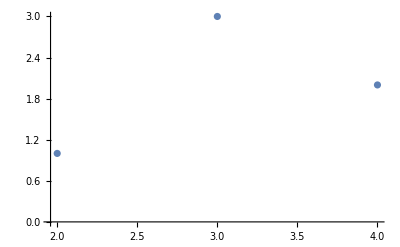

```mathematica
ListPlot[coordinates]
```

ListLinePlot connects the points in the order of the list.

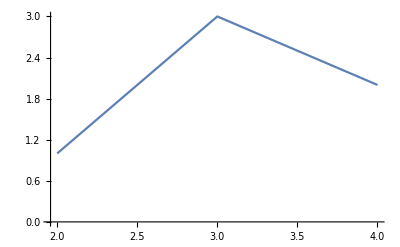

```mathematica
ListLinePlot[coordinates]
```

### Example

Example 2.6.1. Visualize the information in this list named data:

```mathematica
data={{0,0},{0,-1},{-1,1},{1,2},{2,-3},{-3,-5},{-5,8},{8,13}}
```

{{0,0},{0,-1},{-1,1},{1,2},{2,-3},{-3,-5},{-5,8},{8,13}}

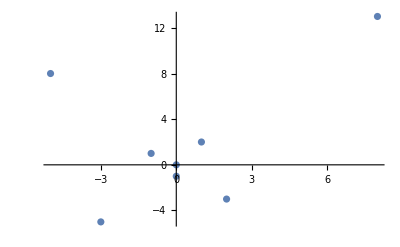

```mathematica
ListPlot[data]
```

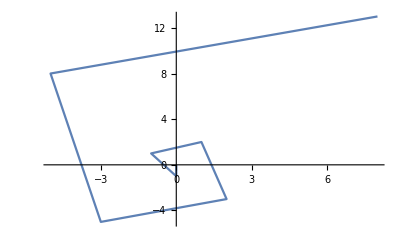

```mathematica
ListLinePlot[data]
```

## 2.7 Visualizing statistics

Here we simulate rolling a six-sided die 200 times.

```mathematica
dice=RandomInteger[{1,6},200]
```

{5,1,5,3,2,2,2,2,1,3,5,3,3,2,4,5,4,5,2,6,3,3,5,5,2,1,4,2,1,2,6,3,6,2,2,6,4,5,1,3,4,6,3,4,2,4,4,6,2,3,5,5,5,3,5,4,2,5,5,1,5,3,6,5,6,5,6,1,3,4,1,4,1,5,2,2,4,2,5,3,3,4,6,5,5,3,4,3,6,4,4,3,4,3,3,5,4,3,1,1,6,5,2,4,1,1,1,1,4,6,2,6,1,1,1,3,4,5,1,6,2,5,2,3,5,4,5,1,4,4,6,6,1,2,4,6,2,6,4,6,3,5,2,6,2,6,4,4,5,3,3,2,4,5,4,3,5,6,2,3,5,6,3,5,2,6,1,6,2,6,2,1,2,3,6,5,1,6,2,3,3,5,2,6,5,6,6,1,4,4,2,5,1,6,1,4,6,5,2,2}

We can take the data and tally how many of each output arise using the Tally command

```mathematica
Tally[dice]
```

{{5,38},{1,27},{3,32},{2,36},{4,33},{6,34}}

We should probably Sort the entries and then use TableForm so that it is easier to read:

```mathematica
TableForm[Sort[Tally[dice]]]
```

1 | 27
2 | 36
3 | 32
4 | 33
5 | 38
6 | 34

Or we can represent the data visually by way of the Histogram command

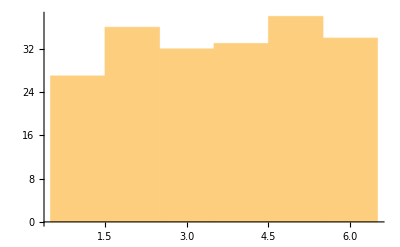

```mathematica
Histogram[dice]
```

## 2.8 Useful list commands

### Length

Length will tell you how many elements there are in the list.

```mathematica
Length[{1,2,3}]
```

3

```mathematica
Length[{1,{2,3}}]
```

2

### Total

Total will sum the values in the list.

```mathematica
Total[{1,2,3}]
```

6

Example : Find the sum of the powers of 10 from 1 to 100000.

```mathematica
powersOfTen=Table[10^i,{i,0,5}]
```

{1,10,100,1000,10000,100000}

```mathematica
Total[powersOfTen]
```

111111